```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/luis/WORK/metabolomics/FBA/Using_WM/with_SA_network

```mathematica
smatrix = Import["cobra_py_iYS854_network/smatrix.txt","Table"];
```

```mathematica
reactions = ReplaceAll[{s_String}:>ToExpression@StringSplit[s,","]]@Import["cobra_py_iYS854_network/reactions.txt","Table"] //Flatten//ToExpression;
```

```mathematica
upper = ReplaceAll[{s_String}:>ToExpression@StringSplit[s,","]]@Import["cobra_py_iYS854_network/upper.txt","Table"] //Flatten//ToExpression;
```

```mathematica
lower = ReplaceAll[{s_String}:>ToExpression@StringSplit[s,","]]@Import["cobra_py_iYS854_network/lower.txt","Table"] //Flatten//ToExpression;
```

```mathematica
sdotr = smatrix.reactions;
```

```mathematica
fluxesCobraPy = ReplaceAll[{s_String}:>ToExpression@StringSplit[s,","]]@Import["cobra_py_iYS854_network/fluxes_solution.txt","Table"] //Flatten//ToExpression;
```

```mathematica
a =FindMaximumpaclet:ref/FindMaximum[{BIOMASS99iYS99wild99type,And@@(Table[sdotr[[i]] <= 0.01,{i,1,Length[smatrix.reactions]} ]~Join~Table[sdotr[[i]] >= -0.01,{i,1,Length[smatrix.reactions]} ]~Join~Table[reactions[[i]] ≤ upper[[i]]  , {i,1,Length[reactions]}]~Join~Table[reactions[[i]] ≥  lower[[i]],
 {i,1,Length[reactions]}])},reactions,Method->"PrincipalAxis"];
l1 ="FindMaximum["<>StringDrop[StringDrop[StringDelete[ a//ToString,WhitespaceCharacter],StringPosition[StringDelete[ a//ToString,WhitespaceCharacter],"[{BIOMASS99iYS99wild99type,0."][[1,1]]],-11];solution = l1//ToExpression;
```

```mathematica
fluxesWM = reactions/.solution[[2]];
```

```mathematica
f[a_]:=StringReplace[a,"99"-> "_"]
```

```mathematica
labels = StringSplit[StringDelete[f@(ToString@reactions),{"{", "}"}],","];
```

```mathematica
labels=Reverse[labels[[Ordering@(Abs@fluxesWM)]]];
fluxesAbWM = Reverse[Abs@fluxesWM[[Ordering@(Abs@fluxesWM)]]];
```

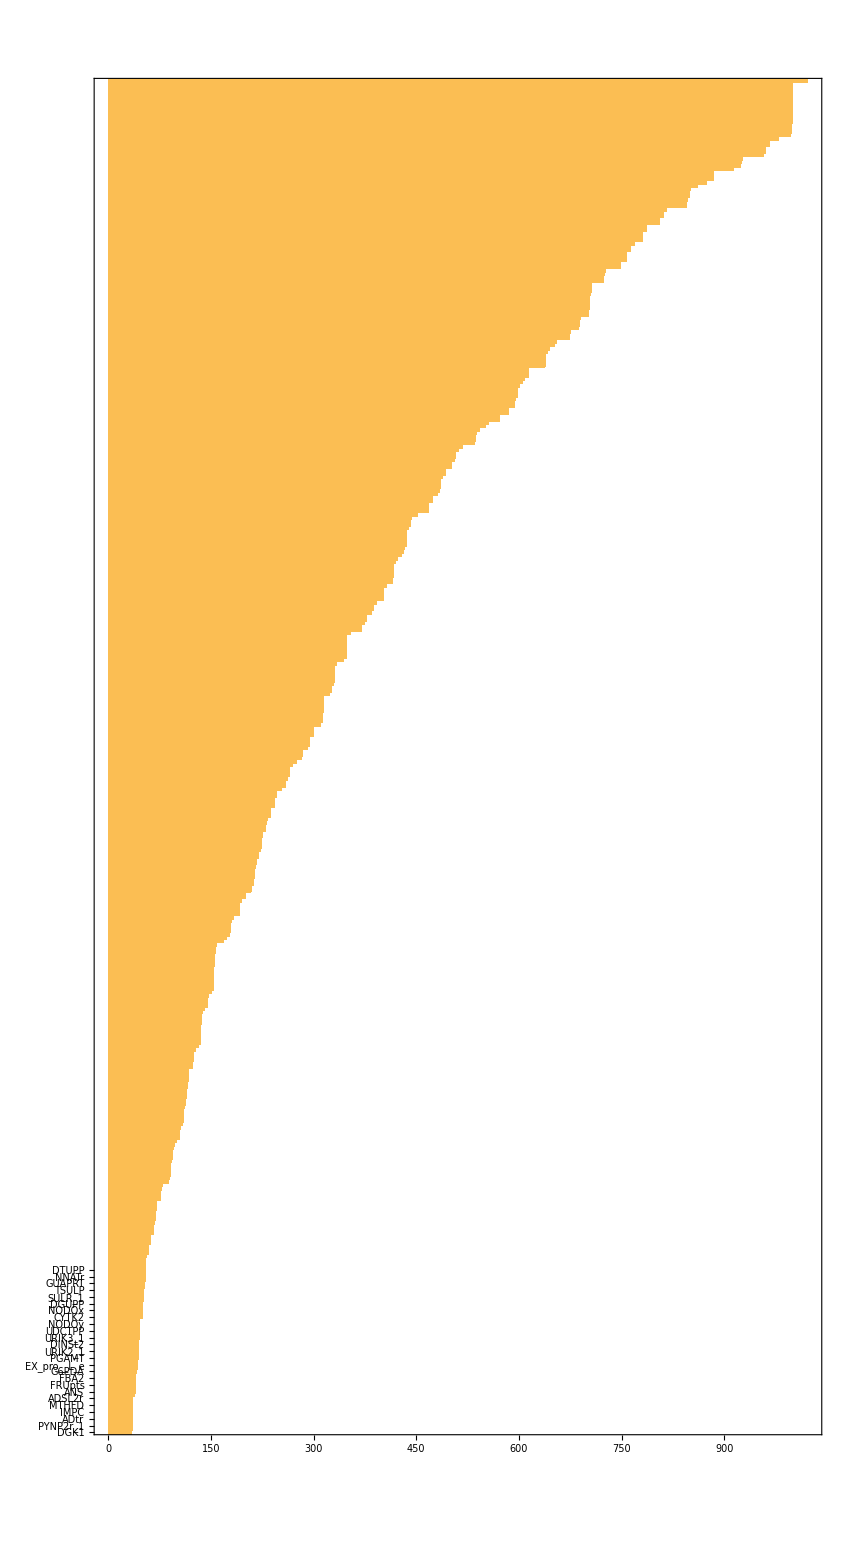

```mathematica
BarChart[Reverse[fluxesAbWM[[1;;400]]], ChartLabels->Placed[Reverse[labels[[1;;400]]],Axis,Rotate[#,0]&], BarOrigin->Left,AspectRatio->5,Frame->True, PlotRange->{All,{8,393}}]
```